## Stability diagram plot

```mathematica
ClearAll["Global`*"];
```

### Defenitions

```mathematica
Eq1=-Sqrt[(Qm/Qp)] (Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));
Eq2=Sqrt[Qp/Qm] (-Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));

Eq3=a (Sqrt[Qm/Qp]+Sqrt[Qp/Qm]) γa+(-Sqrt[((Qm-a^2 Qm)/Qp)]+Sqrt[(Qp-a^2 Qp)/Qm]) γp+(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd);

Ns=((Qm γ+Qp γ+γd) μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

ns=((Qm-Qp) γ μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

ω=Sqrt[Qp/Qm] ((α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ]);

M={{-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),-Sqrt[(Qm/Qp)] (-a γa+Sqrt[1-a^2] γp),-Sqrt[1-a^2] γa-a γp,-a γa+Sqrt[1-a^2] γp,Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (-a γa+Sqrt[1-a^2] γp),-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa-a γp,Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-Sqrt[1-a^2] γa+a γp,a γa+Sqrt[1-a^2] γp,-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qp/Qm] (-a γa-Sqrt[1-a^2] γp),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa+a γp,-Sqrt[(Qp/Qm)] (-a γa-Sqrt[1-a^2] γp),-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};
(*M={{-Sqrt[(Qm/Qp)] (-γa Cos[2 ψ]-γp Sin[2 ψ]),-Sqrt[(Qm/Qp)] (γp Cos[2 ψ]-γa Sin[2 ψ]),-γa Cos[2 ψ]-γp Sin[2 ψ],γp Cos[2 ψ]-γa Sin[2 ψ],Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (γp Cos[2 ψ]-γa Sin[2 ψ]),-Sqrt[(Qm/Qp)] (-γa Cos[2 ψ]-γp Sin[2 ψ]),-γp Cos[2 ψ]+γa Sin[2 ψ],-γa Cos[2 ψ]-γp Sin[2 ψ],Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-γa Cos[2 ψ]+γp Sin[2 ψ],γp Cos[2 ψ]+γa Sin[2 ψ],-Sqrt[(Qp/Qm)] (-γa Cos[2 ψ]+γp Sin[2 ψ]),Sqrt[Qp/Qm] (-γp Cos[2 ψ]-γa Sin[2 ψ]),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-γp Cos[2 ψ]-γa Sin[2 ψ],-γa Cos[2 ψ]+γp Sin[2 ψ],-Sqrt[(Qp/Qm)] (-γp Cos[2 ψ]-γa Sin[2 ψ]),-Sqrt[(Qp/Qm)] (-γa Cos[2 ψ]+γp Sin[2 ψ]),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};*)
```

#### Tests:

```mathematica
M.{0,Sqrt[Qp],0,Sqrt[Qm],0,0}//FullSimplify[#,Assumptions-> {Qp>0&&Qm>0}]&
```

{0,0,0,0,0,0}

```mathematica
M//FullSimplify[#,Assumptions-> {Qp>0&&Qm>0}]&//MatrixForm
```

(√(Qm/Qp) (√(1-a^2) γa+a γp) | √(Qm/Qp) (a γa-√(1-a^2) γp) | -√(1-a^2) γa-a γp | -a γa+√(1-a^2) γp | √Qp κ | √Qp κ
√(Qm/Qp) (-a γa+√(1-a^2) γp) | √(Qm/Qp) (√(1-a^2) γa+a γp) | a γa-√(1-a^2) γp | -√(1-a^2) γa-a γp | √Qp α κ | √Qp α κ
-√(1-a^2) γa+a γp | a γa+√(1-a^2) γp | √(Qp/Qm) (√(1-a^2) γa-a γp) | -√(Qp/Qm) (a γa+√(1-a^2) γp) | √Qm κ | -√Qm κ
-a γa-√(1-a^2) γp | -√(1-a^2) γa+a γp | √(Qp/Qm) (a γa+√(1-a^2) γp) | √(Qp/Qm) (√(1-a^2) γa-a γp) | √Qm α κ | -√Qm α κ
-(2 √Qp γ (2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | -(2 √Qm γ (2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | -(1+Qm+Qp) γ | (Qm-Qp) γ
-(2 √Qp γ (2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | (2 √Qm γ (2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | (Qm-Qp) γ | -(Qm+Qp) γ-γd)

### For gradient method

```mathematica
avars={a5,a4,a3,a2,a1};
vars={Qp,Qm,ψ};
params={Λ,γp};
charpolycoefs={-2 Qm Qp γ (γa^2+γp^2) Cos[2 ψ] ((Sqrt[Qm^3 Qp]-Sqrt[Qm Qp^3]) (γ γa-α γd γp)+(Qm-Qp) (Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) κ Cos[2 ψ]+(Qm-Qp) Sqrt[Qm Qp] (γ γa+α γd γp) Cos[4 ψ]+α ((Qm+Qp) (Qm+Qp+4 Qm Qp) γ+(Qm-Qp)^2 γd) κ Sin[2 ψ]+Qm Sqrt[Qm Qp] α γ γa Sin[4 ψ]+Qp Sqrt[Qm Qp] α γ γa Sin[4 ψ]+4 (Qm Qp)^(3/2) α γ γa Sin[4 ψ]-4 (Qm Qp)^(3/2) γ γp Sin[4 ψ]-Qm Sqrt[Qm Qp] γd γp Sin[4 ψ]-Qp Sqrt[Qm Qp] γd γp Sin[4 ψ]),γ (-2 (Qm-Qp) (Qm Qp)^(3/2) γa (γa^2+γp^2) Cos[2 ψ]^3+2 (α γa+γp) Sin[2 ψ] ((4 Qm (Qm Qp)^(3/2) γ+2 (Qm Qp)^(3/2) (γ+2 Qp γ-γd)+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (γ+γd)) κ+2 Qm Qp (-Qm+Qp) γd γp Sin[2 ψ])+2 Qm Cos[2 ψ]^2 (2 Qp (γa^2 (2 (Qm-Qp) γ+(1+Qm+Qp) γd)-(Qm+Qp+4 Qm Qp) α γ γa γp+((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd) γp^2)+Qp (-Qm+Qp) (Qm+Qp) (γa^2+γp^2) κ-((Qm Qp)^(3/2)+Sqrt[Qm Qp^5]) (α γa-γp) (γa^2+γp^2) Sin[2 ψ])+Cos[2 ψ] (8 Qm (Qm Qp)^(3/2) γ (γa-α γp) κ+2 (γ+γd) ((Sqrt[Qm^5 Qp]-3 Sqrt[Qm Qp^5]) γa-(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) α γp) κ-(Qm Qp)^(3/2) (Qp α γp (γa^2+γp^2)+4 (γ-γd) (γa+α γp) κ+8 Qp γ (3 γa+α γp) κ)+Qm Qp (Qp Sqrt[Qm Qp] α γp (γa^2+γp^2) Cos[4 ψ]+2 Sin[2 ψ] (2 ((Qm+Qp+4 Qm Qp) α γ γa^2+γa (Qp (γ-3 γd)+Qm (γ-4 Qp γ-γd)) γp+(Qm-Qp) α γd γp^2)-(Qm^2+Qp^2) α (γa^2+γp^2) κ+Qm Sqrt[Qm Qp] α γp (γa^2+γp^2) Sin[2 ψ])))),Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qm α γ γa γp+((1+Qm+3 Qp) γ+γd) γp^2)+4 Qp γ (Qm (γ+4 Qp γ-γd)+Qp (γ+γd)) κ-2 γ (8 (Qm Qp)^(3/2) γ γa+4 Sqrt[Qm^3 Qp] γ γa+4 Sqrt[Qm Qp] γa γd+4 Sqrt[Qm^3 Qp] γa γd+4 Sqrt[Qm Qp^3] γa γd-Sqrt[Qm^5 Qp] γa κ+3 Sqrt[Qm Qp^5] γa κ+Sqrt[Qm^5 Qp] α γp κ+Sqrt[Qm Qp^5] α γp κ) Cos[2 ψ]+Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qp α γ γa γp+((1+3 Qm+Qp) γ+γd) γp^2) Cos[4 ψ]+γ (2 (8 (Qm Qp)^(3/2) γ γp+4 Sqrt[Qm Qp^3] γd γp+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (α γa+γp) κ) Sin[2 ψ]+Qm Qp ((Qm+Qp) α γa^2-2 Qp γa γp+(Qm-Qp) α γp^2) Sin[4 ψ]),-4 γa ((Sqrt[Qm Qp]+2 Sqrt[Qm^3 Qp]+Sqrt[Qm Qp^3]) γ+Sqrt[Qm Qp] γd) Cos[2 ψ]+Qm Qp (γa^2+γp^2) Cos[2 ψ]^2+4 γ (γd+Qm (γ+4 Qp γ+γd)+Qp (γ+γd+Qp κ)+Sqrt[Qm Qp^3] γp Sin[2 ψ]),2 (γ+2 Qm γ+2 Qp γ+γd-Sqrt[Qm Qp] γa Cos[2 ψ]),1};
charpolycoefs=charpolycoefs[[1;;5]];
stateqns={
κ(Ns+ns - 1)-γa Sqrt[Qm/Qp] Cos[2 ψ]- γp Sqrt[Qm/Qp]Sin[2 ψ], κ  α(Ns+ns - 1)+γa Sqrt[Qm/Qp] Sin[2 ψ]-γp Sqrt[Qm/Qp]Cos[2 ψ]-ω,κ (Ns-ns- 1)-γa Sqrt[Qp/Qm]Cos[2 ψ]+ γp Sqrt[Qp/Qm] Sin[2 ψ],κ  α(Ns-ns - 1)-γa Sqrt[Qp/Qm]Sin[2 ψ]-γp Sqrt[Qp/Qm]Cos[2 ψ]-ω,-γ(Ns -Λ)-γ(Ns+ns) Qp-γ(Ns-ns) Qm,-γd ns-γ(Ns+ns) Qp+γ(Ns-ns) Qm};
stateqns[[2]]=stateqns[[2]]-stateqns[[4]]//FullSimplify;
stateqns=Drop[stateqns,{4}];
HwM={
{a1,a3,a5,0},
{1,a2,a4,0},
{0,a1,a3,a5},
{0,1,a2,a4}};
dDda=Table[D[Det[HwM],avars[[i]]],{i,1,5}];
dadx=Table[D[charpolycoefs[[i]],vars[[j]]],{i,1,5},{j,1,3}];
dadp=Table[D[charpolycoefs[[i]],params[[j]]],{i,1,5},{j,1,2}];
solNn = Solve[stateqns[[4;;5]]==0,vars[[4;;5]]][[1]]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&ψ∈Reals}]&;
stat3eqns = stateqns[[1;;3]]/.solNn//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&ψ∈Reals}]&;
dfdx=Table[D[stat3eqns[[i]],vars[[j]]],{i,1,3},{j,1,3}]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
dfdp=Table[D[stat3eqns[[i]],params[[j]]],{i,1,3},{j,1,2}]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
```

Part::take: Cannot take positions 4 through 5 in {Qp,Qm,ψ}.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

Part::pkspec1: The expression #2 cannot be used as a part specification.

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

Part::pkspec1: The expression #2 cannot be used as a part specification.

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression #2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

Part::pkspec1: The expression #2 cannot be used as a part specification.

### Solution

```mathematica
(*Solving stationary problem*)
	
γa=-0.01;
γ=1.;
γp=53.3669;
κ=300.;
γd=50.;
α=3.;
μ=5;
Qp0=0.9;
Qm0=0.1;
a0=0.205;

γa=-0.1;
γ=1.;
κ=600.;
γd=50.;
α=5.;
γp=0.1439394597656346;
μ=1.00397;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;

Qm0v2=1/2 (-1-Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ);
Qp0v2=1/2 (-1+Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ);
tan0v2=((α γa-γp) Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2])/(2 γ (γa+α γp)^2 κ (-1+μ));
a0v2=tan0v2/Sqrt[1+tan0v2^2];
If[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2<0,Qm0v2=(μ-1)/2;Qp0v2=(μ-1)/2;a0v2=0;]
Qm0v2=(μ-1)/2*0.1;Qp0v2=(μ-1)/2*0.9;a0v2=-0.1;
(*Nsol=NSolve[{Eq1==0,Eq2==0,Eq3==0},{Qp,Qm,a}]//Select[#,AllTrue[{Qp,Qm,a}/.#,#∈Reals&]&]&;*)
(*If[Length[Nsol]==0,Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}],
ElSol=Select[Nsol,(Abs[Qp-Qm]/.#)>10^-6&];
If[Length[ElSol]==0,Nsol=Nsol[[1]],Nsol=ElSol[[1]]]
];*)
(*β=((α γa-γp)-(γa+α γp) a0)/((α γa-γp) +(γa+α γp) a0);
Qp0=(μ-1)/(1+β);
Qm0=β Qp0;*)
Nsol2=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0v2,N[10^-8],10.},{Qm,Qm0v2,N[10^-8],10.},{a,a0v2,-1.,1.}}]
(*Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];*)
(*Ns-1/.Nsol
ns/.Nsol
Nsol*)
```

{Qp→0.677214,Qm→0.00990104,a→-0.200219}

```mathematica
Ns/.Nsol2
```

1.01291

```mathematica
ns/.Nsol2
```

0.

```mathematica
a0v2
```

-10.1996

```mathematica
{Eq1,Eq2,Eq3}/.Nsol2
```

{6.71685×10^-14,-7.28306×10^-14,4.54747×10^-13}

```mathematica
Qp0v2
```

0.

```mathematica
Sin[ArcTan[a/.Nsol]]
```

{-0.205778,-0.205778,0.205778,0.205778}

```mathematica
-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2
```

-257.413

```mathematica
{Qp0v2,Qm0v2}
```

{0.02096,0.02096}

```mathematica
(*Evaluating charpoly*)

p=CoefficientList[CharacteristicPolynomial[M/.Nsol2,λ],λ];
p[[1]]=0;
(*p=-CoefficientList[CharacteristicPolynomial[(tmp2/.Nsol),λ],λ];*)
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)
If[AllTrue[p,NonNegative],
If[AllTrue[Dets,NonNegative],
Print["System is stable"];
Print[p//MatrixForm];
Print[Dets//MatrixForm],
Print["Some Hurwitz determinants are negative:"];
Print[p//MatrixForm];
Print[Dets//MatrixForm]
],
Print["Some p < 0"];
Print[p//MatrixForm];
Print[Dets//MatrixForm];
]
```

System is stable

(0
2.78727×10^8
1.08785×10^7
336824.
7137.01
21.3852
1)

(2.39304×10^9
3.2988×10^24)

```mathematica
Nsol
```

{Qp→0.350028,Qm→0.350028,a→0}

```mathematica
If[Positive[-CharacteristicPolynomial[tmp2,λ]],If[AllTrue[Dets,Positive],Print["System is stable"];Print[p];Print[Dets],Print["Some Hurwitz determinants are negative:"];Print[p];Print[Dets]],Print["Some p < 0"];Print[p]]
```

If[Positive[-CharacteristicPolynomial[tmp2,λ]],If[AllTrue[Dets,Positive],Print[System is stable];Print[p];Print[Dets],Print[Some Hurwitz determinants are negative:];Print[p];Print[Dets]],Print[Some p < 0];Print[p]]

```mathematica
p
```

{1.91066×10^7,422612.,68199.,1328.33,52.4401,1}

```mathematica
({{3.232764872790355*^-8}, {1.910655999879378*^7}, {422611.74144311715}, {68199.01081752068}, {1328.32937396901}, {52.44011333711123}, {1}})({{52.44011333711123}, {1458.7321024281991}, {-6.073344503642392*^7}, {-4.313731141096*^12}, {-8.24205628660157*^19}}){Qp->0.3500283342778091,Qm->0.35002833427780905,a->-1.0848001355988288*^-16}
```

### Plotting by pixels v0

```mathematica
γa=-0.01;
γ=1.;
γp=10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;
ysub={Sqrt[1-a^2]-> -Sqrt[1-a^2]};
Nμ=100;
Nγp=100;
μs=CoordinateBoundsArray[{{1.,5.}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{1.,2.}},Into[Nγp]]//Flatten//Power[10,#]&;
result=ConstantArray[0,{Nγp,Nμ}];
result2=ConstantArray[0,{Nγp,Nμ}];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
μ=μs[[i]];
γp=γps[[j]];

Nsol=FindRoot[({Eq1,Eq2,Eq3})==0,{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p[[1]]=0;
If[AllTrue[p[[2;;]],Positive],
	Dets=ConstantArray[0,2];
Dets[[1]]=p[[6]]*p[[5]]-p[[4]]; (*D2*)
Dets[[2]]=Det[{
{p[[6]],p[[4]],p[[2]],0},
{1,p[[5]],p[[3]],0},
{0,p[[6]],p[[4]],p[[2]]},
{0,1,p[[5]],p[[3]]}}];(*D4*)

If[AllTrue[Dets,Positive],
If[Abs[Qp-Qm/.Nsol]<10^-8,result[[i,j]]=1,result[[i,j]]=0.7],
result[[i,j]]=0;
]
(*result[[i,j]]=0;
If[Dets[[1]]>0,result[[i,j]]=0.3,];
If[Dets[[2]]>0,result[[i,j]]=result[[i,j]]+0.7,] ***=> D4 fails****)
,
result[[i,j]]=0;
];
Dets=ConstantArray[0,5];
HurwM={
{p[[6]],p[[4]],p[[2]],0,0},
{1,p[[5]],p[[3]],0,0},
{0,p[[6]],p[[4]],p[[2]],0},
{0,1,p[[5]],p[[3]],0},
{0,0,p[[6]],p[[4]],p[[2]]}};
Dets[[1]]=HurwM[[1,1]];
Dets[[2]]=Det[HurwM[[1;;2,1;;2]]];
Dets[[3]]=Det[HurwM[[1;;3,1;;3]]];
Dets[[4]]=Det[HurwM[[1;;4,1;;4]]];
Dets[[5]]=Det[HurwM[[1;;5,1;;5]]];
If[AllTrue[Dets,Positive],
If[Abs[Qp-Qm/.Nsol]<10^-8,result2[[i,j]]=1,result2[[i,j]]=0.7],
result2[[i,j]]=0;
];
If[Not[AllTrue[({Eq1,Eq2,Eq3}/.Nsol//Chop)==  0]],result[[i,j]]=-1]
]
];
Image[Reverse[result]]
Image[Reverse[result2]]
Image[Reverse[Abs[result2-result]]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

```mathematica
Select[Abs[result2-result]//Flatten,#≠  0&]
```

{}

```mathematica
Select[result//Flatten,#==-1&]
```

{}

```mathematica
newres=Table[If[result[[i,j]]>0.5,1,0],{i,1,Nμ},{j,1,Nγp}];
contour=Abs[newres[[2;;,2;;]]-newres[[;;-2,2;;]]]+Abs[newres[[2;;,2;;]]-newres[[2;;,;;-2]]];
rgb=ConstantArray[0,{Nμ,Nγp,3}];
rgb[[;;,;;,2]]=newres;
rgb[[2;;,2;;,1]]=contour;
Image[Reverse[rgb]]
```

-Graphics-

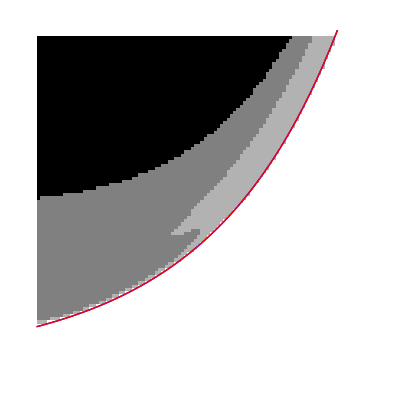

```mathematica
ap=ArrayPlot[1-Reverse[result]];
Mu[γp_]:=(κ+γa)*(α *γ *κ+α *γ *γa-γ *γp+γp *γd)/(γ *κ *(α *κ+α *γa-γp));
MuMine[γp_]:=((γa+κ) (γa^2 γd+γ γa (α γp+κ)+γp (-γ γp+γd γp+α γ κ)))/(γ κ (-γp^2+γa κ+α γp (γa+κ)));
Diff[γp_]:=(MuMine[γp]-Mu[γp])/MuMine[γp];

lp=Plot[(Mu[10*10^(x/Nγp)]-1)/5*Nμ,{x,0,Nγp},PlotStyle-> {Red,Thick}];
lmp=Plot[(MuMine[10*10^(x/Nγp)]-1)/5*Nμ,{x,0,Nγp},PlotStyle-> {Blue,Thick}];
Show[ap,lmp,lp,PlotRange-> {{0,Nγp},{0,Nμ}}]
```

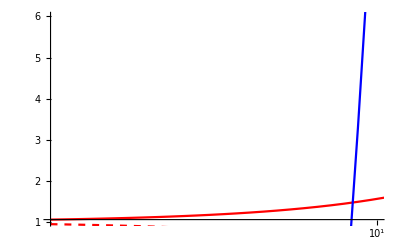

```mathematica
pl1 = Plot[1+γd*x/(γ (α κ - x)),{x,1,100},PlotStyle->Red,ScalingFunctions-> {"Log10",None}];
pl2 =Plot[1-γd/γ+2α x/γ,{x,1,100},PlotStyle->Blue,ScalingFunctions-> {"Log10",None}];
pl3 = Plot[1-γd*x/(γ (α κ + x)),{x,1,100},PlotStyle->{Red,Dashed},ScalingFunctions-> {"Log10",None}];
pl4 =Plot[1-γd/γ-2α x/γ,{x,1,100},PlotStyle->{Blue,Dashed},ScalingFunctions-> {"Log10",None}];
Show[pl1,pl2,pl3,pl4,PlotRange->{{0,1},{1,6}}]
```

```mathematica
oldresult=result;
```

### Plotting bound

```mathematica
Clear["Global`*"]
```

```mathematica
CheckStability[κ_,α_,γ_,γd_,γp_,γa_,μ_,Qp0_,Qm0_,a0_]:=Module[{Eq1,Eq2,Eq3,M,Dets,Nsol,ElSol, Ns, ns,p,Qp0v2,Qm0v2,a0v2,tan0v2},

Eq1=-Sqrt[(Qm/Qp)] (Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));
Eq2=Sqrt[Qp/Qm] (-Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));

Eq3=a (Sqrt[Qm/Qp]+Sqrt[Qp/Qm]) γa+(-Sqrt[((Qm-a^2 Qm)/Qp)]+Sqrt[(Qp-a^2 Qp)/Qm]) γp+(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd);
Ns=((Qm γ+Qp γ+γd) μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);ns=((Qm-Qp) γ μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

M={{-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),-Sqrt[(Qm/Qp)] (-a γa+Sqrt[1-a^2] γp),-Sqrt[1-a^2] γa-a γp,-a γa+Sqrt[1-a^2] γp,Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (-a γa+Sqrt[1-a^2] γp),-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa-a γp,Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-Sqrt[1-a^2] γa+a γp,a γa+Sqrt[1-a^2] γp,-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qp/Qm] (-a γa-Sqrt[1-a^2] γp),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa+a γp,-Sqrt[(Qp/Qm)] (-a γa-Sqrt[1-a^2] γp),-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};

Qm0v2=1/2 (-1-Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ);
Qp0v2=1/2 (-1+Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ);
If[μ>1,
tan0v2=((α γa-γp) Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2])/(2 γ (γa+α γp)^2 κ (-1+μ)),
tan0v2=0];
a0v2=tan0v2/Sqrt[1+tan0v2^2];

If[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2<0,Qm0v2=(μ-1)/2;Qp0v2=(μ-1)/2;a0v2=0;];
If[Qm0v2==0,Qm0v2=10^-7];
If[Qp0v2==0,Qp0v2=10^-7];
Nsol=FindRoot[({Eq1,Eq2,Eq3})==0,{{Qp,Qp0v2,N[10^-8],10.},{Qm,Qm0v2,N[10^-8],10.},{a,a0v2,-1.,1.}}];

(*Nsol=NSolve[{Eq1==0,Eq2==0,Eq3==0},{Qp,Qm,a}]//Select[#,AllTrue[{Qp,Qm,a}/.#,#∈Reals&]&]&;
If[Length[Nsol]==0,Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}],
ElSol=Select[Nsol,(Abs[Qp-Qm]/.#)>10^-6&];
If[Length[ElSol]==0,Nsol=Nsol[[1]],Nsol=ElSol[[1]]]
];*)


p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p[[1]]=0;
If[AllTrue[p[[2;;]],Positive],
	Dets=ConstantArray[0,2];
Dets[[1]]=p[[6]]*p[[5]]-p[[4]]; (*D2*)
Dets[[2]]=Det[{
{p[[6]],p[[4]],p[[2]],0},
{1,p[[5]],p[[3]],0},
{0,p[[6]],p[[4]],p[[2]]},
{0,1,p[[5]],p[[3]]}}];(*D4*)

	If[AllTrue[Dets,Positive],
{1,Nsol},
{0,Nsol}],
{0,Nsol}
]
];
```

```mathematica
γa=-0.1;
γ=1.;
κ=600.;
γd=50.;
α=5.;
Nth=6.25*10^-6;
Ntr=5.935*10^-6;

γp=10;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;

(*Initial grid test*)
Nμ=100;
Nγp=100;
μmin=1.;
μmax=(1.01*Nth-Ntr)/(Nth-Ntr);
γpmin=2π*10^-2;
γpmax=2π*1.;
accuracy=1.*^-5;

μs=CoordinateBoundsArray[{{μmin,μmax}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{Log10[γpmin],Log10[γpmax]}},Into[Nγp]]//Flatten//Power[10,#]&;

result=ConstantArray[0,{Nμ,Nγp}];
MuX[γpp_]:=((γa+κ) (γa^2 γd+γ γa (α γpp+κ)+γpp (-γ γpp+γd γpp+α γ κ)))/(γ κ (-γpp^2+γa κ+α γpp (γa+κ)));
t1=AbsoluteTime[];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
If[μs[[i]]<MuX[γps[[j]]],result[[i,j]]=1,
res=CheckStability[κ,α,γ,γd,γps[[j]],γa,μs[[i]],Qp0,Qm0,a0];
result[[i,j]]=res[[1]];
(*Qp0=Qp/.res[[2]];Qm0=Qm/.res[[2]];a0=a/.res[[2]];*)
(*If[(Abs[Qp-Qm]/.res[[2]])<10^-8,result[[i,j]]=result[[i,j]]*0.5];*)
If[Not[AllTrue[({Eq1,Eq2,Eq3}/.res[[2]]//Chop)==  0]],result[[i,j]]=-1];];
]];
Print[AbsoluteTime[]-t1];
If[Length[Select[result//Flatten,#<0&]]>0,Print["Somewhere stationary equations were not properly solved!"]];
contour=Abs[result[[2;;,2;;]]-result[[;;-2,2;;]]]+Abs[result[[2;;,2;;]]-result[[2;;,;;-2]]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

34.092814

```mathematica
Image[Reverse[result]]
```

-Graphics-

```mathematica
Image[Reverse[result[[1;;4,8;;20]]]]
```

-Graphics-

```mathematica
result[[3,19]]
γps[[19]]
μs[[3]]
```

0

0.143939

1.00397

```mathematica
ap=ArrayPlot[1-Reverse[result]];
Mu[γp_]:=(κ+γa)*(α *γ *κ+α *γ *γa-γ *γp+γp *γd)/(γ *κ *(α *κ+α *γa-γp));
MuX[γp_]:=((γa+κ) (γa^2 γd+γ γa (α γp+κ)+γp (-γ γp+γd γp+α γ κ)))/(γ κ (-γp^2+γa κ+α γp (γa+κ)));
MuYγaZ[γp_]:=1+2α γp/γ - γd/γ;
Diff[γp_]:=(MuX[γp]-Mu[γp])/MuX[γp];

(*lp=Plot[(Mu[γpmin*(γpmax/γpmin)^(x/Nγp)]-μmin)/(μmax-μmin)*Nμ,{x,0,Nγp},PlotStyle-> {Red,Thick}];*)
lmp=Plot[(MuX[γpmin*(γpmax/γpmin)^(x/Nγp)]-μmin)/(μmax-μmin)*Nμ,{x,0,Nγp},PlotStyle-> {Red,Thick},PlotRange-> {{0,Nγp},{0,Nμ}}];
lmpY=Plot[(MuYγaZ[γpmin*(γpmax/γpmin)^(x/Nγp)]-μmin)/(μmax-μmin)*Nμ,{x,0,Nγp},PlotStyle-> {Blue,Thick},PlotRange-> {{0,Nγp},{0,Nμ}}];
Show[ap,lmp,lmpY,PlotRange-> {{0,Nγp},{0,Nμ}}]
```

-Graphics-

```mathematica
(*cnt=Thinning[contour];*)
cnt=ContourDetect[result/.x_-> x-0.5];

(*find initial pixel*)
pt={0,0};
notfind=True;
For[i=1,i≤ Nμ,i++,
If[cnt[[i,1]]==1,pt={i,1};notfind=False;Break,]
];
If[notfind,(*TODO search fo other bound*),];
(*creating initial line*)
used=ConstantArray[0,Dimensions[cnt]];
used[[pt[[1]],pt[[2]]]]=1;
points={pt};
nomore=False;
While[Not[nomore],
pt=Nearest[DeleteCases[DeleteCases[Flatten[Table[{pt[[1]]+i,pt[[2]]+j},{i,-1,1},{j,-1,1}],1],x_/;x[[1]]<1||x[[1]]≥ Nμ||x[[2]]<1||x[[2]]≥ Nγp],x_/;cnt[[x[[1]],x[[2]]]]==0],pt,
DistanceFunction->((used[[First[#2],Last[#2]]]-0.0001*First[#2]-0.0004*Last[#2])&)][[1]];
If[used[[pt[[1]],pt[[2]]]]==1,nomore=True;Print[pt],used[[pt[[1]],pt[[2]]]]=1;points=Append[points,pt]];
]
```

{6,99}

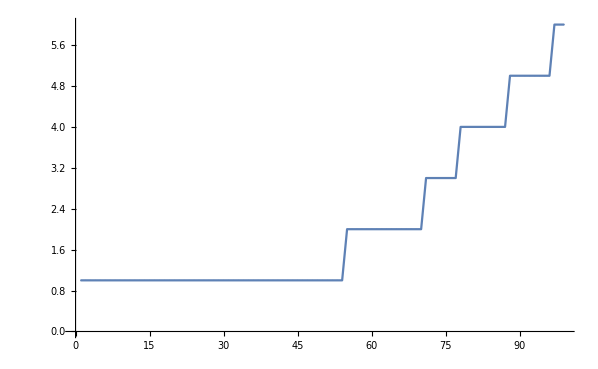

```mathematica
ListPlot[Reverse[points,2],PlotMarkers->{Automatic,1},Joined->True]
```

```mathematica
(*Search with bisection method until given precision*)
accuratePoints={};
p2s={};
p1s={};
For[i=2,i< Length[points],i++,
pt=points[[i]];
Δxy=points[[i+1]]-points[[i-1]];
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.7//N;
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.7//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res=result[[pt[[1]],pt[[2]]]];
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];

If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=1,k≤ 30&&res1==res&&res2==res,k++,
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1*k//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1*k//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt,pt2=pt;];
];

(*If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*2//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]+1);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]+1)/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*2//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]+1);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]+1)/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
];*)
If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
Print["All points for binary search are still in one domain"];
Print[pt];
];
p1s=Append[p1s,pt1];
p2s=Append[p2s,pt2];
If[res1+res==1,res2=res;pt2=pt,res1=res;pt1=pt];
While[Norm[pt1-pt2]>accuracy,
ptmid=(pt1+pt2)/2;
μmid=μmin+(μmax-μmin)/Nμ*(ptmid[[1]]);
If[μmid<1,μmid=1];
γpmid=γpmin*(γpmax/γpmin)^((ptmid[[2]])/Nγp);
resmid=CheckStability[κ,α,γ,γd,γpmid,γa,μmid,Qp0,Qm0,a0][[1]];
If[resmid==res2,pt2=ptmid,pt1=ptmid];
];
accuratePoints=Append[accuratePoints,(pt1+pt2)/2];
];
```

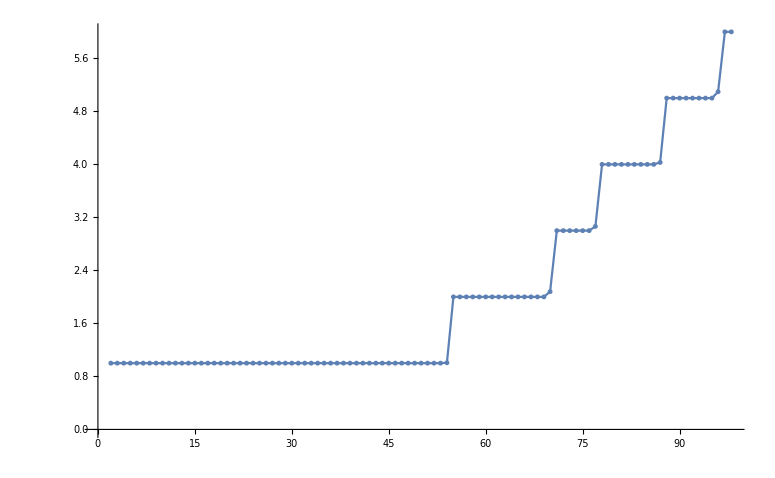

```mathematica
ListPlot[Reverse[accuratePoints,2],PlotMarkers->{Automatic,5},Joined->True]
```

```mathematica
temppoints=Table[points[[i]]+{1,1},{i,1,Length[points]}];
```

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[initfinepts,2].

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[initfinepts,2.].

General::stop: Further output of Reverse::normal will be suppressed during this calculation.

ListPlot::lpn: Reverse[initfinepts,2.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

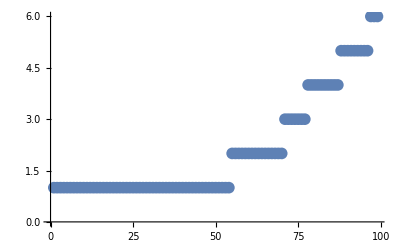
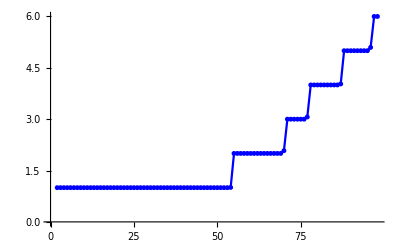
Show[-Graphics-,-Graphics-,ListPlot[Reverse[initfinepts,2],PlotStyle→RGBColor[1, 0, 0],PlotMarkers→{Automatic,5}],PlotRange→{{295,350},{1,40}},ImageSize→{500,500},AspectRatio→Full]

```mathematica
grpts=ListPlot[Reverse[points,2],PlotMarkers->{Automatic,12},Joined->False];
grnewpts=ListPlot[Reverse[accuratePoints,2],Joined-> True,PlotMarkers-> {Automatic,5},PlotStyle->Blue];
grp1s=ListPlot[Reverse[p1s,2],PlotStyle->Green];
grp2s=ListPlot[Reverse[p2s,2],PlotStyle->Red];
intergr=ListPlot[Reverse[initfinepts,2],PlotStyle->Red,PlotMarkers->{Automatic,5}];
Show[grpts,grnewpts,intergr,PlotRange->{{295,350},{1,40}},ImageSize->{500,500},AspectRatio->Full]
```

```mathematica
(*Interpolating fine boundary*)
```

```mathematica
PointNum=100;
sums=Prepend[Table[Sum[Norm[accuratePoints[[i]]-accuratePoints[[i-1]]]^2,{i,2,j}],{j,2,Length[accuratePoints]}],0];
interp=Interpolation[Transpose[{sums,accuratePoints}],Method->"Spline"];
initfinepts=Table[interp[Last[sums]/(PointNum-1)*i],{i,0,PointNum-1}];
```

```mathematica
(*Additional fine boundary search*)
finepts={};
p1s={};
p2s={};
For[i=2,i< Length[initfinepts],i++,
pt=initfinepts[[i]];
Δxy=initfinepts[[i+1]]-initfinepts[[i-1]];
pt1=initfinepts[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.5//N;
pt2=initfinepts[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.5//N;
μ=μmin+(μmax-μmin)/Nμ*(pt[[1]]);
γp=γpmin*(γpmax/γpmin)^((pt[[2]])/Nγp);
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res=CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0][[1]];
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];

If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],For[k=1,k≤15&&res1==res&&res2==res,k++,pt1=initfinepts[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1*k//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=initfinepts[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1*k//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];];
If[res==res1,pt1=pt,pt2=pt;];];

(*If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=2,k≤ 10&&res1==res,k++,
pt1=initfinepts[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.2*k//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt;
For[k=2,k≤ 10&&res2==res,k++,
pt2=initfinepts[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.2*k//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
],pt2=pt;];

];*)
If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
Print["All points for binary search are still in one domain. Ignoring point:"];
Print[i];
Print[pt];
Print[{pt1,pt2}],

p1s=Append[p1s,pt1];
p2s=Append[p2s,pt2];
If[res1+res==1,res2=res;pt2=pt,res1=res;pt1=pt];
While[Norm[pt1-pt2]>accuracy,
ptmid=(pt1+pt2)/2;
μmid=μmin+(μmax-μmin)/Nμ*(ptmid[[1]]);
If[μmid<1,μmid=1];
γpmid=γpmin*(γpmax/γpmin)^((ptmid[[2]])/Nγp);
resmid=CheckStability[κ,α,γ,γd,γpmid,γa,μmid,Qp0,Qm0,a0][[1]];
If[resmid==res2,pt2=ptmid,pt1=ptmid];
];
finepts=Append[finepts,(pt1+pt2)/2];
];
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

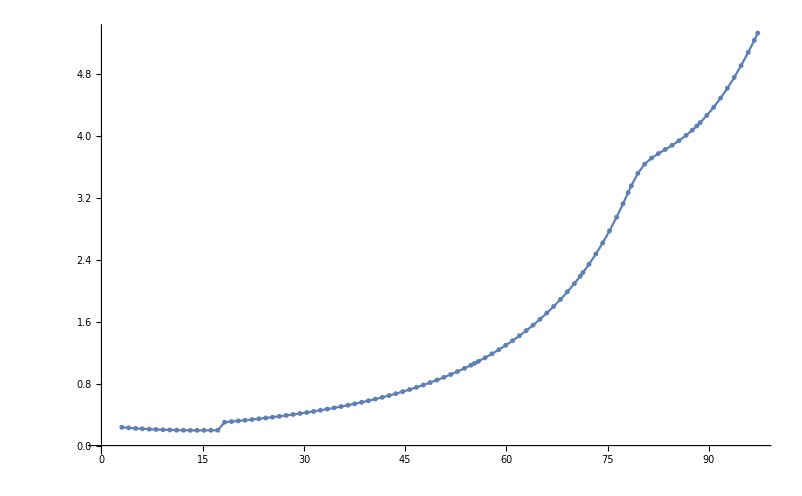

```mathematica
ListPlot[Reverse[finepts,2],PlotMarkers->{Automatic,5},Joined->True]
```

```mathematica
(*Additional smoothing*)
PointNum2=1000;
accuracy2=10^-7;
sums2=Prepend[Table[Sum[Norm[finepts[[i]]-finepts[[i-1]]],{i,2,j}],{j,2,Length[finepts]}],0];
interp2=Interpolation[Transpose[{sums2,finepts}],Method->"Spline"];
initfinepts2=Table[interp2[Last[sums2]/(PointNum2)*i],{i,0,PointNum2}];
finepts2={};
p1s={};
p2s={};
For[i=2,i< Length[initfinepts2],i++,
pt=initfinepts2[[i]];
Δxy=initfinepts2[[i+1]]-initfinepts2[[i-1]];
pt1=initfinepts2[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.05//N;
pt2=initfinepts2[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.05//N;
μ=μmin+(μmax-μmin)/Nμ*(pt[[1]]);
γp=γpmin*(γpmax/γpmin)^((pt[[2]])/Nγp);
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res=CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0][[1]];
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];

If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=1,k≤ 10&&res1==res&&res2==res,k++,
pt1=initfinepts2[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.003*k//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=initfinepts2[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.003*k//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt,pt2=pt;];
];

(*If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=3,k≤ 10&&res1==res,k++,
pt1=initfinepts2[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.005*k//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt;
For[k=3,k≤ 10&&res2==res,k++,
pt2=initfinepts2[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.005*k//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
],pt2=pt;];

];*)
If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
Print["All points for binary search are still in one domain. Ignoring point:"];
Print[i];
Print[pt];
Print[{pt1,pt2}],

p1s=Append[p1s,pt1];
p2s=Append[p2s,pt2];
If[res1+res==1,res2=res;pt2=pt,res1=res;pt1=pt];
While[Norm[pt1-pt2]>accuracy2,
ptmid=(pt1+pt2)/2;
μmid=μmin+(μmax-μmin)/Nμ*(ptmid[[1]]);
If[μmid<1,μmid=1];
γpmid=γpmin*(γpmax/γpmin)^((ptmid[[2]])/Nγp);
resmid=CheckStability[κ,α,γ,γd,γpmid,γa,μmid,Qp0,Qm0,a0][[1]];
If[resmid==res2,pt2=ptmid,pt1=ptmid];
];
finepts2=Append[finepts2,(pt1+pt2)/2];
];
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
(*Evaluating real boundary in terms of γp and μ*)
initboundary=Table[{μmin+(μmax-μmin)/Nμ*(finepts2[[i,1]]),γpmin*(γpmax/γpmin)^((finepts2[[i,2]])/Nγp)},{i,1,Length[finepts2]}];
boundaryScaled=Table[{initboundary[[i,1]]*(1-Ntr/Nth)+Ntr/Nth,initboundary[[i,2]]/(2π)},{i,1,Length[initboundary]}];
```

```mathematica
SetDirectory["D:\\work\\VCSEL experiments\\TeXи\\graphs"];
boundary=Reverse[boundaryScaled,2];
Save["fig[k_a_gd][600 50 5].m",{γa,γ,γd,κ,α,Nth,Ntr,boundary}]
```

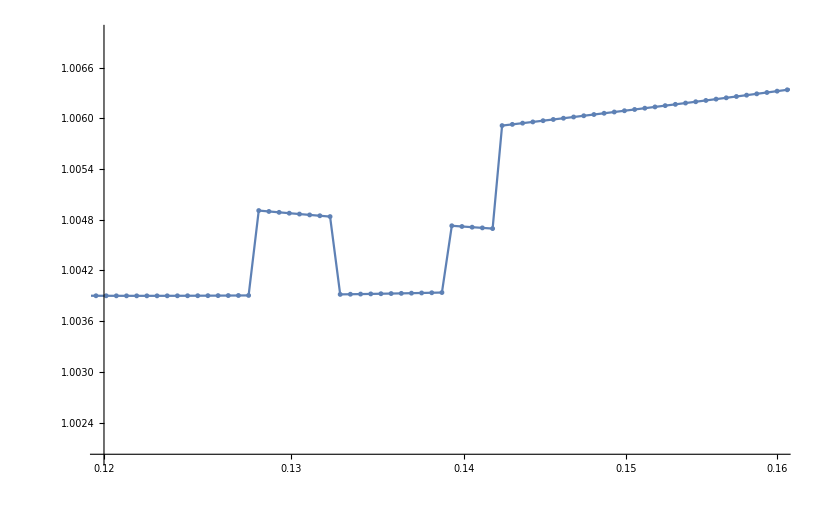

```mathematica
ListLinePlot[Reverse[initboundary,2],ScalingFunctions->{"Log10",None},PlotMarkers->{Automatic,5},PlotRange->{{0.12,0.16},{1.002,1.007}}]
```

```mathematica
CheckStability[κ,α,γ,γd,0.13,γa,1.00565,Qp0,Qm0,a0]
```

{0,{Qp→0.00522399,Qm→0.000405399,a→-0.700102}}

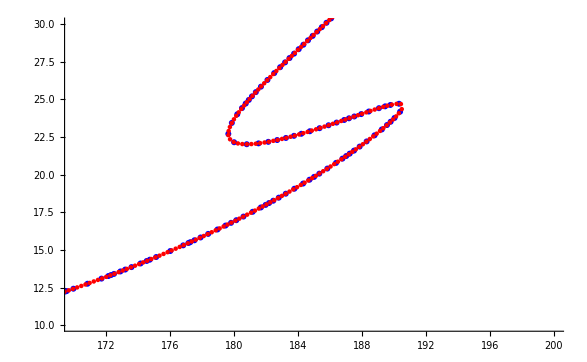

```mathematica
tmpgr1=ListPlot[Reverse[finepts,2],Joined-> False,PlotStyle->Blue];
tmpgr2=ListPlot[Reverse[finepts2,2],Joined-> False,PlotStyle->Red];
Show[tmpgr1,tmpgr2,PlotRange->{{170,200},{10,30}}]
```

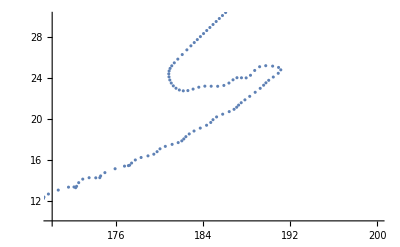

```mathematica
ListPlot[Reverse[initfinepts,2],Joined-> False,PlotRange->{{170,200},{10,30}}]
```

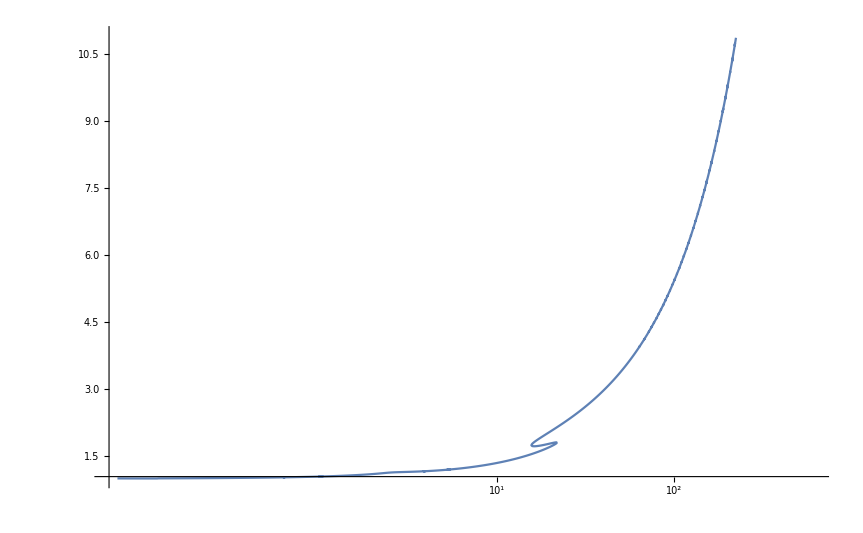

```mathematica
(*Plotting boundary*)
ListPlot[Reverse[boundary,2],Joined-> True,ScalingFunctions->{"Log10",None},PlotRange->{{γpmin,γpmax},{μmin,μmax}}]
```

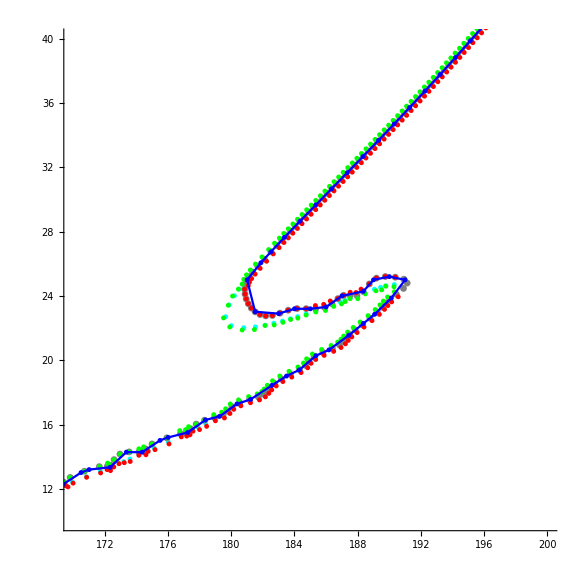

```mathematica
gr1=ListPlot[Reverse[finepts,2],PlotMarkers->{Automatic,5},PlotStyle->Cyan];
gr2=ListPlot[Reverse[initfinepts,2],PlotMarkers->{Automatic,7},PlotStyle->Gray];
p1gr=ListPlot[Reverse[p1s,2],PlotMarkers->{Automatic,5},PlotStyle->Green];
p2gr=ListPlot[Reverse[p2s,2],PlotMarkers->{Automatic,5},PlotStyle->Red];
pt=ListPlot[Reverse[{{49.49141013980161,38.97557295787219},{49.184755339570366,39.10897716181132},{48.89666389409548,39.28266753911388},{48.72596050561139,38.2204349285255},{49.64355017352934,39.997519395097136}},2],PlotMarkers->{Automatic,3},PlotStyle->Red];
Show[gr1,gr2,p1gr,p2gr,grnewpts,PlotRange->{{170,200},{10,40}},ImageSize-> {400,400},AspectRatio->Full]
```

```mathematica
tstpts={{49.49141013980161,38.97557295787219},{49.184755339570366,39.10897716181132},{48.89666389409548,39.28266753911388}};
dxy=tstpts[[3]]-tstpts[[1]];
tst=tstpts[[2]]+{dxy[[2]],-dxy[[1]]}/Sqrt[dxy[[1]]^2+dxy[[2]]^2]//N
tst-tstpts[[2]]
```

{49.6436,39.9975}

{0.458795,0.888542}

```mathematica
{48.72596050561139,38.2204349285255},{49.64355017352934,39.997519395097136}
```

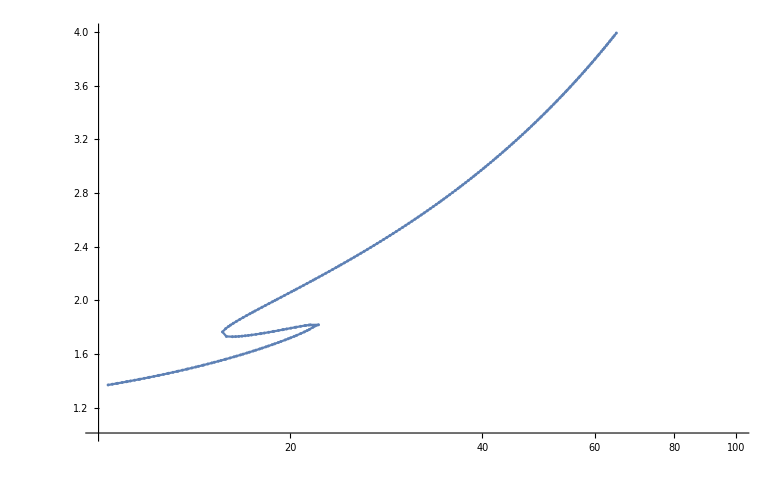

```mathematica
ListPlot[Reverse[boundary,2],Joined-> True,PlotMarkers->{Automatic,3},ScalingFunctions->{"Log10",None},PlotRange->{{γpmin,γpmax},{μmin,μmax}}]
```

```mathematica
listp=ListPlot[Reverse[accuratePoints,2]];
listp1=ListPlot[Reverse[p1s,2],PlotStyle->Blue];
listp2=ListPlot[Reverse[p2s,2],PlotStyle->Red];
Show[ap,lmp,lmpY,listp,PlotRange-> {{0,Nγp},{0,Nμ}}]
```

-Graphics-

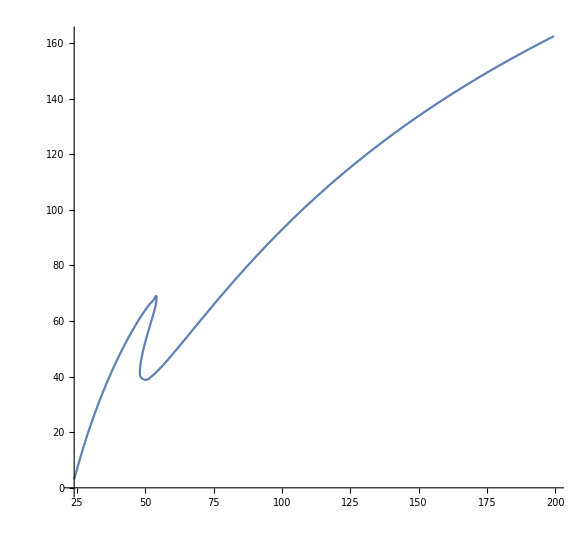

```mathematica
sums=Prepend[Table[Sum[Norm[accuratePoints[[i]]-accuratePoints[[i-1]]],{i,2,j}],{j,2,Length[accuratePoints]}],0];
ParametricPlot[Interpolation[Transpose[{sums,accuratePoints}],Method->"Spline"][t],{t,0,Last[sums]}]
```

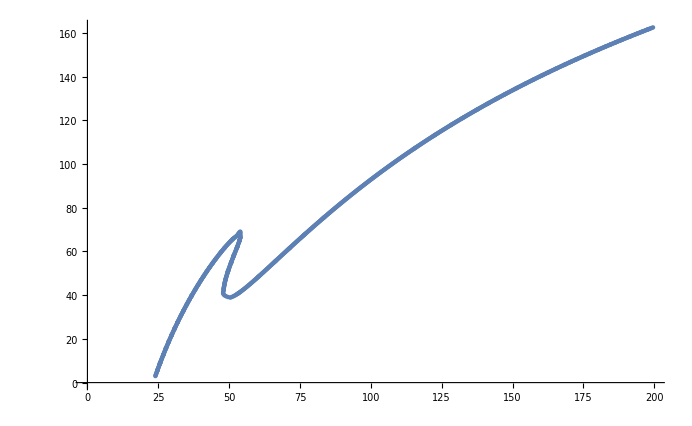

```mathematica
ListPlot[initfinepts]
```

```mathematica
Table[Sum[Norm[accuratePoints[[i]]-accuratePoints[[i-1]]],{i,2,j}],{j,2,Length[accuratePoints]}]
```

{1.38014,2.74721,3.11177,4.56813,5.93245,6.23254,7.27492,8.65768,10.0186,10.4088,11.8315,13.1899,13.5535,14.9995,16.3555,16.7097,18.1619,19.5156,19.8786,21.3191,22.6707,23.0611,24.4715,25.8211,26.2583,27.6193,28.967,29.8652,31.2117,31.6236,33.0062,34.3513,35.2477,36.5919,37.4877,38.8311,39.2238,40.6216,41.9641,42.859,44.201,45.0956,46.4373,47.3318,48.6734,49.5678,50.9096,51.8042,53.1463,54.0412,55.384,56.2795,57.6233,58.5197,60.1153,61.2117,62.1103,63.4599,64.3609,65.8993,67.3314,68.4401,69.3579,70.8807,73.0309,75.5588,76.0375,77.0607,77.36,78.7291,80.1741,80.547,81.9083,83.3089,84.354,84.63,85.9918,87.4838,87.8096,89.1752,90.5984,91.632,91.9148,93.2904,94.7161,95.7375,96.7553,97.7691,98.7786,99.7837,100.785,102.693,105.247,107.149,108.526,109.455,110.737,112.151,113.566,114.982,116.399,117.816,118.974,119.896,121.363,122.782,124.201,125.621,127.041,128.174,129.093,130.591,132.011,133.43,134.85,135.988,136.908,138.398,139.817,141.236,142.655,143.817,144.74,146.2,147.617,149.035,150.452,151.869,153.285,154.453,155.381,156.826,158.241,159.657,161.072,162.487,163.902,165.317,166.732,168.146,169.561,170.975,172.39,173.804,175.218,176.632,178.047,179.461,180.875,182.289,183.704,185.119,186.533,187.948,189.363,190.779,192.194,193.61,195.027,196.443,197.86,199.227,200.151,201.404,202.822,204.24,205.66,207.079,208.439,209.357,210.631,212.052,213.474,214.897,216.225,217.139,218.457,219.882,221.244,222.154,223.448,224.876,226.305,227.611,228.519,229.88,231.311,232.6,233.506,234.894,236.221,237.125,238.483,239.837,240.74,242.079,243.518,244.801,245.702,247.123,248.406,249.306,250.734,252.006,252.906,254.352,255.604,256.502,257.85,258.749,260.157,261.442,262.34,263.795,265.032,265.929,267.274,268.171,269.515,270.412,271.826,273.1,273.996,275.339,276.235,277.693,278.921,279.817,281.159,282.054,283.397,284.292,285.634,286.529,287.871,288.766,290.232,291.45,292.344,293.686,294.58,295.922,296.816,298.158,299.053,300.637}

```mathematica
point=accuratePoints[[1]]-{0.00001,0}
```

{23.974,3.}

```mathematica
μ=μmin+(μmax-μmin)/Nμ*(point[[1]]);
γp=γpmin*(γpmax/γpmin)^((point[[2]])/Nγp);
CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0]
```

{1,{Qp→0.244943,Qm→0.123096,a→-0.069379}}

```mathematica
CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0]
```

{0,{Qp→0.647738,Qm→0.041918,a→-0.181763}}

```mathematica
Norm[pt1-pt2]
```

6.

```mathematica
pt1-pt2
```

{2.68328,-5.36656}

```mathematica
i=2;
pt=points[[i]];
Δxy=points[[i+1]]-points[[i-1]];
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]//N;
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]//N;
μ=μmin+(μmax-μmin)/Nμ*pt1[[1]]
γp=γpmin*(γpmax/γpmin)^(pt1[[2]]/Nγp)
```

1.65683

10.364

```mathematica
{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]//N
```

{0.894427,-0.447214}

```mathematica
{μs[[pt[[1]]+1]],γps[[pt[[2]]+1]]}
{μs[[pt[[1]]+2]],γps[[pt[[2]]+2]]}
```

{1.63,10.4713}

{1.66,10.7152}

```mathematica
Image[Reverse[cnt]]
```

-Graphics-

```mathematica
f=ListInterpolation[points,InterpolationOrder->2];

Plot[f[x],{x,0,4}]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2,1}.

-Graphics-

```mathematica
Clear[X,Y,p2,L];
X={xm1,0,xp1};
Y={ym1,0,yp1};
L[j_,x_]:=Product[If[i==j,1,(x−X[[i]])/(X[[j]]−X[[i]])],{i,1,3}];
p2[x_]:=Sum[Y[[i]]*L[i,x],{i,1,3}]
```

```mathematica
D[p2[x],x]/.{x-> 0}//FullSimplify
```

(-xp1^2 ym1+xm1^2 yp1)/(xm1 (xm1-xp1) xp1)

```mathematica
p2[x]
```

(x (x-xp1) ym1)/(xm1 (xm1-xp1))+(x (x-xm1) yp1)/(xp1 (-xm1+xp1))

```mathematica
g=Graph[Sort/@{{1,1}<->{1,2},{1,2}<->{3,2},{1,2}<->{1,1},{1,2}<->{1,1},{1,2}<->{2,3},{3,2}<->{3,3},{3,3}<->{2,3},{2,3}<->{3,4}}//DeleteDuplicates,PlotTheme->"IndexLabeled"]
```

-Graphics-

```mathematica
FindHamiltonianPath[g]
```

{{3,4},{2,3},{3,3},{3,2},{1,2},{1,1}}

```mathematica
HighlightGraph[g,PathGraph[%]]
```

-Graphics-

```mathematica
ArrayMesh[cnt]
```

### Plotting by pixels v2

```mathematica
γa=-0.01;
γ=1.;
γp=-10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;
Nμ=100;
Nγp=100;
μs=CoordinateBoundsArray[{{1.,6.}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{1.,2.}},Into[Nγp]]//Flatten//Power[10,#]&;
result=ConstantArray[0,{Nγp,Nμ}];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
μ=μs[[i]];
γp=γps[[j]];
Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];

p=-CoefficientList[CharacteristicPolynomial[(tmp3/.{Λ-> μ}/.Nsol),λ],λ];

If[AllTrue[p,Positive],
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)

If[AllTrue[Dets,Positive],
result[[i,j]]=0;
If[Dets[[1]]>0,result[[i,j]]=0.3,];
If[Dets[[2]]>0,result[[i,j]]=result[[i,j]]+0.7,] 
,
result[[i,j]]=0
],
If[oldresult[[i,j]]>0,Print[i," ",j],]
]
]];
Image[Reverse[result]]
```

Power::infy: Infinite expression 1/0. encountered.

CharacteristicPolynomial::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0. encountered.

CharacteristicPolynomial::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

CharacteristicPolynomial::inf: Input matrix contains an infinite entry.

General::stop: Further output of CharacteristicPolynomial::inf will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {0.107997,0.906551,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.123634,0.910422,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.139076,0.914214,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

-Graphics-

```mathematica
Image[Reverse[oldresult-result]]
Image[Reverse[oldresult]]
```

-Graphics-

-Graphics-

```mathematica
μ=μs[[100]];
γp=γps[[83]];
Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];
p=charpolycoefs/.Nsol;
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)
```

```mathematica
p
```

{1.02348×10^10,1.18555×10^8,-1.30236×10^6,35269.8,121.689}